```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`;
```

```mathematica
dat=<<"blobs.txt";
```

```mathematica
xnList=Flatten@{Range[1,10],10*Range[2,10]};
```

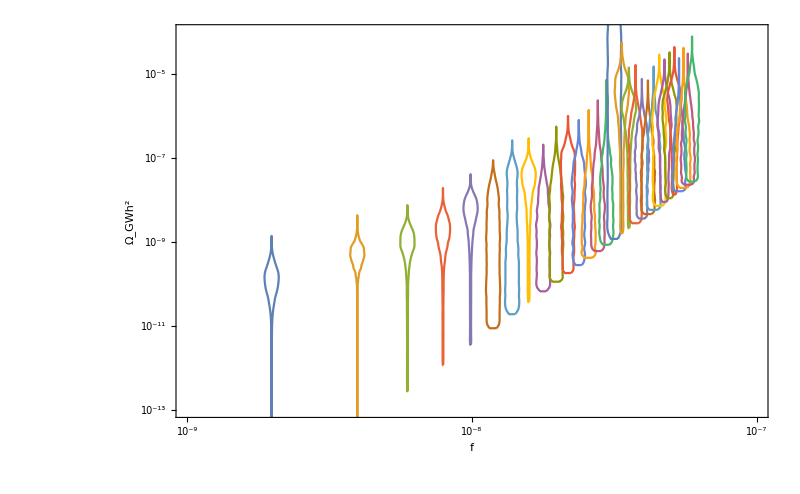

```mathematica
PTA1=Show[
ListLogLogPlot[dat,Joined->True],
ImageSize->800,Frame->True,
PlotRange->{Log@{10^-9,10^-7},Log@{10^-13,10^-4}},
FrameLabel->{f,"Ω_GWh^2"},
FrameTicks->{
{
Table[{Log[10^n],If[EvenQ[n],"\!\(\*SuperscriptBox[\(10\), \("<>ToString[n]<>"\)]\)",""]},{n,-12,-4}]
,
Table[{Log[10^n],""},{n,-12,-4,2}]
},
{
Table[{Log[n*10^-9],If[MemberQ[{1,10,100},n],"\!\(\*SuperscriptBox[\(10\), \(-"<>ToString@Round@Abs@Log[10,n*10^-9]<>"\)]\)",""]},{n,xnList}],
Table[{Log[n*10^-9],""},{n,xnList}]
}
},
PlotRangePadding->None,AxesOrigin->Log@{10^-9,10^-13},BaseStyle->FontSize->24,FrameStyle->FontFamily->"Times",LabelStyle->GrayLevel[0]
]
```

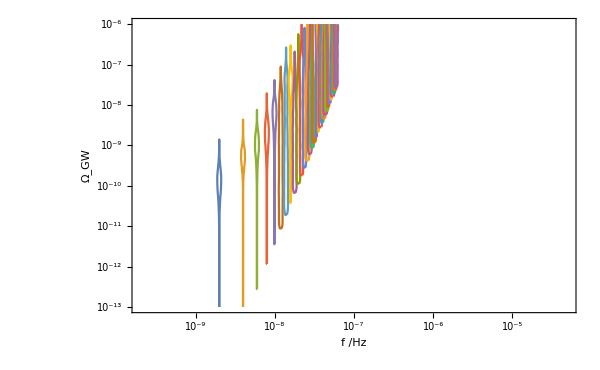

```mathematica
PTA2=ListLogLogPlot[dat,Joined->True,PlotStyle->ColorData[97],Epilog->Table[{Opacity[0.3],ColorData[97][i],Polygon@dat[[i]]},{i,Length@dat}],PlotRange->{{2 10^-10,5 10^-5},{10^-13,10^-6}},Joined->True,Frame->True,PlotStyle->{Thickness[0.005],Blue},BaseStyle->FontSize->18,FrameStyle->FontFamily->"Times",LabelStyle->GrayLevel[0],Axes->False,ImageSize->600,GridLines->Automatic,FrameLabel->{f"/Hz","Ω_GW"}]
```

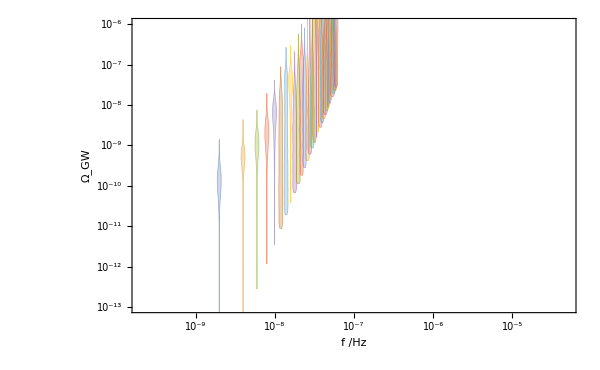

```mathematica
PTA2=ListLogLogPlot[{},PlotRange->{{2*10^-10,5*10^-5},{10^-13,10^-6}},Frame->True,BaseStyle->FontSize->18,FrameStyle->FontFamily->"Times",LabelStyle->GrayLevel[0],Axes->False,ImageSize->600,GridLines->Automatic,FrameLabel->{f "/Hz","\!\(\*SubscriptBox[\(Ω\), \(GW\)]\)"},Epilog->Table[{Opacity[0.3],ColorData[97][i],EdgeForm[Directive[Opacity[0.6],ColorData[97][i],AbsoluteThickness[0.5]]],Polygon[Log@dat[[i]]]},{i,Length[dat]}]]
```

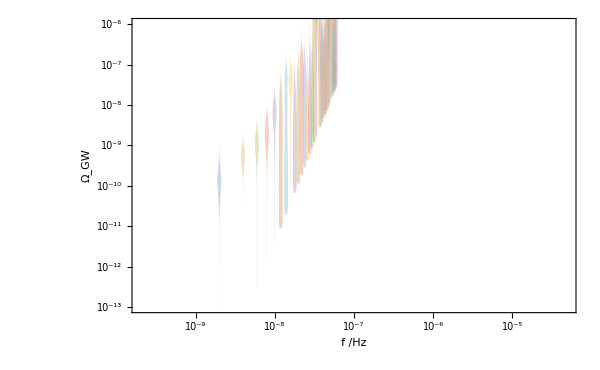

```mathematica
PTA3=ListLogLogPlot[{},PlotRange->{{2*10^-10,5*10^-5},{10^-13,10^-6}},Frame->True,BaseStyle->FontSize->18,FrameStyle->FontFamily->"Times",LabelStyle->GrayLevel[0],Axes->False,ImageSize->600,GridLines->Automatic,FrameLabel->{f "/Hz","\!\(\*SubscriptBox[\(Ω\), \(GW\)]\)"},Epilog->Table[{Opacity[0.3],ColorData[97][i],Polygon[Log@dat[[i]]]},{i,Length[dat]}]]
```

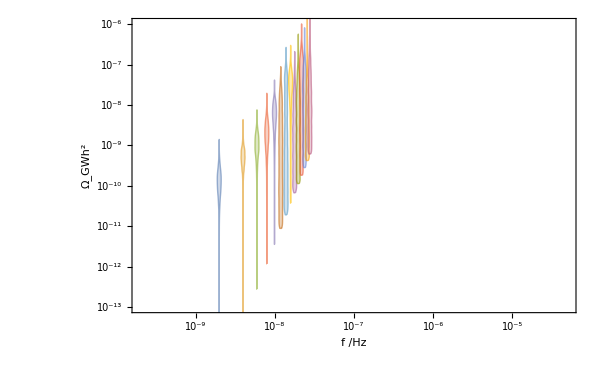

```mathematica
PTA14=ListLogLogPlot[{},PlotRange->{{2*10^-10,5*10^-5},{10^-13,10^-6}},Frame->True,BaseStyle->FontSize->18,FrameStyle->FontFamily->"Times",LabelStyle->GrayLevel[0],Axes->False,ImageSize->600,GridLines->Automatic,FrameLabel->{f "/Hz","\!\(\*SubscriptBox[\(Ω\), \(GW\)]\)h^2"},Epilog->Table[{Opacity[0.3],ColorData[97][i],EdgeForm[Directive[Opacity[0.6],ColorData[97][i],AbsoluteThickness[1.0]     ]],Polygon[Log@dat[[i]]]},{i,14}]]
```